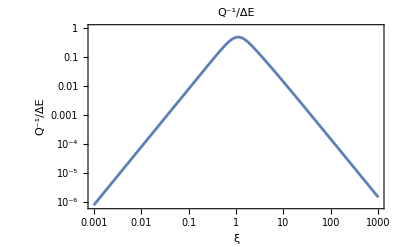

```mathematica
QwoHeatFlow =Abs[ 6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) ];
LogLogPlot[QwoHeatFlow,{ξ,0.001,1000},PlotLabel->"Q^-1/ΔE", Frame->True,FrameLabel->{ξ,"Q^-1/ΔE"}]
```

```mathematica
QHeatFlow=Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]; (*sapphire*)
```

d=1.1,1.3,1.7

3/4 Abs[(-2 ξ (Cos[2.1 ξ] Cosh[0.1 ξ]+Cos[0.1 ξ] Cosh[2.1 ξ])-Cosh[2.1 ξ] Sin[0.1 ξ]+Cosh[0.1 ξ] Sin[2.1 ξ]-Cos[2.1 ξ] Sinh[0.1 ξ]+Cos[0.1 ξ] Sinh[2.1 ξ])/(ξ^3 (Cos[2.2 ξ]+Cosh[2.2 ξ]))]

3/4 Abs[(-2 ξ (Cos[2.3 ξ] Cosh[0.3 ξ]+Cos[0.3 ξ] Cosh[2.3 ξ])-Cosh[2.3 ξ] Sin[0.3 ξ]+Cosh[0.3 ξ] Sin[2.3 ξ]-Cos[2.3 ξ] Sinh[0.3 ξ]+Cos[0.3 ξ] Sinh[2.3 ξ])/(ξ^3 (Cos[2.6 ξ]+Cosh[2.6 ξ]))]

3/4 Abs[(-2 ξ (Cos[2.7 ξ] Cosh[0.7 ξ]+Cos[0.7 ξ] Cosh[2.7 ξ])-Cosh[2.7 ξ] Sin[0.7 ξ]+Cosh[0.7 ξ] Sin[2.7 ξ]-Cos[2.7 ξ] Sinh[0.7 ξ]+Cos[0.7 ξ] Sinh[2.7 ξ])/(ξ^3 (Cos[3.4 ξ]+Cosh[3.4 ξ]))]

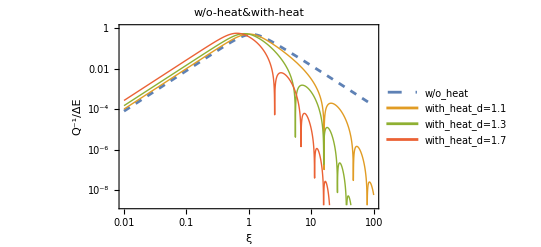

```mathematica
Q11=QHeatFlow/.{d->1.1}
Q13=QHeatFlow/.{d->1.3}
Q17=QHeatFlow/.{d->1.7}
HeatFlowg=LogLogPlot[{QwoHeatFlow,Q11,Q13,Q17},{ξ,0.01,100},PlotLabel->"w/o-heat&with-heat", Frame->True,FrameLabel->{ξ,"Q^-1/ΔE"},PlotStyle->{Dashed,Thick,Thick,Thick},PlotLegends->Placed[{"w/o_heat","with_heat_d=1.1","with_heat_d=1.3","with_heat_d=1.7"},{0.3,0.25}],GridLinesStyle->LightGray,GridLines->Full]
```